```mathematica
(*
  Powered By Walter
期末试题第二题，使用的是Romanoff法
Forever Black Widow, Natasha Romanoff.
*)
```

```mathematica
h=0.02;
```

```mathematica
f[x_]:=Exp[2*x^2]
```

```mathematica
F[x_]:=4+16*x^2
```

```mathematica
Fx[x_]:=18*Exp[6*x-12]/(1+Exp[3*x-6])^2
```

```mathematica
Gx[x_]:=-9*Exp[3x-6]/(1+Exp[3x-6])^2
```

```mathematica
x=Table[x,{x,0,5,0.02}];
x//MatrixForm;
```

```mathematica
y0=f[x];
y0//MatrixForm;
```

```mathematica
y1=Table[0,251];
y1//MatrixForm;
```

```mathematica
y1[[1]]=f[0.0];
y1[[2]]=f[0.02];
```

```mathematica
For[i=2,
i≤250,
i++,
y1[[i+1]]=((2+5*h^2/6*F[x[[i]]])*y1[[i]]-(1-h^2/12*F[x[[i-1]]])*y1[[i-1]])/(1-h^2/12*F[x[[i+1]]])]
```

```mathematica
ListLinePlot[{y0,y1}]
```

-Graphics-

```mathematica
y=Table[0,251];
y//MatrixForm;
```

```mathematica
y[[1]]=0.99752738;
y[[2]]=0.99737488;
```

```mathematica
For[i=2,
i≤250,
i++,
y[[i+1]]=((2+5*h^2/6*Fx[x[[i]]])*y[[i]]-(1-h^2/12*Fx[x[[i-1]]])*y[[i-1]]+h^2/12*(Gx[x[[i-1]]]+10*Gx[x[[i]]]+Gx[x[[i+1]]]))/(1-h^2/12*Fx[x[[i+1]]])]
```

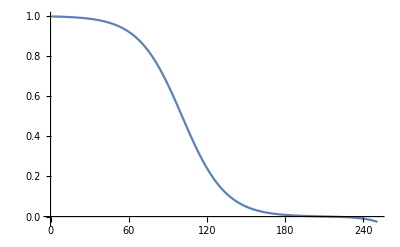

```mathematica
ListLinePlot[y]
```